# Equation of the line that passes through the given point and is perpendicular to the given line

```mathematica
Subscript[x, P_]:=P[[1]];Subscript[y, P_]:=P[[2]];
```

```mathematica
A={2,3};
```

```mathematica
y1[x_]=2x+3;
```

```mathematica
m1=Coefficient[y1[x],x, 1]
```

2

```mathematica
m2=-1/m1
```

-1/2

```mathematica
y2[x_]=m2(x-Subscript[x, A])+Subscript[y, A]//Simplify
```

4-x/2

```mathematica
PointA=ListPlot[{A},PlotRange->{{-5,5},{-5,5}},MeshStyle->Red,PlotMarkers->{Automatic,Medium},AspectRatio->1];
```

```mathematica
LineD=Plot[{y1[x],y2[x]},{x,-5,5},PlotRange->{{-5,5},{-5,5}},AspectRatio->1];
```

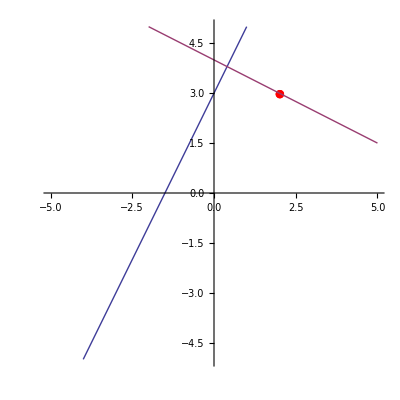

```mathematica
Show[PointA,LineD]
```